```mathematica
Remove["Global`*"]
```

Data Manipulations.

The period of a pendulum made of a light string of length l and massive bob is given by t where g is the acceleration due to gravity. Data d gives values of time in seconds, for ten swings of the pendulum, at given lengths in inches.

```mathematica
d = {{70,26.75},{59,24.86},{47,21.81},{33,18.29},{26,16.13},{19,13.78},{8,8.87}}
```

{{70,26.75},{59,24.86},{47,21.81},{33,18.29},{26,16.13},{19,13.78},{8,8.87}}

```mathematica
t = (2 Pi )* Sqrt[l/g]
```

2 √(l/g) π

```mathematica
s = Solve[t==T, g][[1]]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{g→(4 l π^2)/T^2}

Values of length converted to meters

```mathematica
lv = d[[All,1]]*(2.54)
```

{177.8,149.86,119.38,83.82,66.04,48.26,20.32}

Values of time in seconds

```mathematica
tv = d[[All,2]]
```

{26.75,24.86,21.81,18.29,16.13,13.78,8.87}

Values of g for each data point

```mathematica
gv=g/. s/.{T->tv, l->lv}
```

{9.80943,9.57289,9.90786,9.89191,10.0207,10.0334,10.1961}

Average value of g

```mathematica
ag = Mean[gv]
```

9.91891

```mathematica
std = StandardDeviation[gv]
```

0.197018

Average value of g plus and minus standard deviation

```mathematica
c1 = ag + std
c2 = ag - std
```

10.1159

9.72189

```mathematica
t1= (2 Pi )* Sqrt[l/ag] (*Period at average gravity*)
t2=2 Pi Sqrt[l/c1] (*Period at average gravity + standard deviation*)
t3=2 Pi  Sqrt[l/c2] (*Period at average gravity - standard deviation*)
```

1.99502 √l

1.9755 √l

2.01514 √l

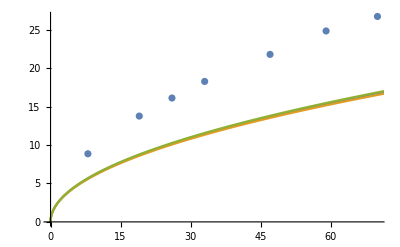

```mathematica
Show[ListPlot[d], Plot[{t1, t2, t3}, {l,0,80}]]
```